```mathematica
B=Import["/home/gutiloluis/61Monograph/mas-gillespie/b.dat"];
Kr=Import["/home/gutiloluis/61Monograph/mas-gillespie/kr.dat"];
Taup=Import["/home/gutiloluis/61Monograph/mas-gillespie/taup.dat"];
```

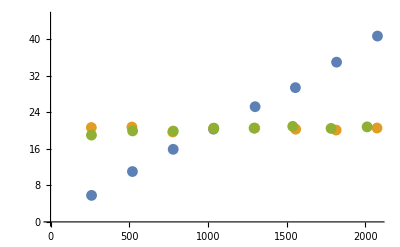

```mathematica
p1=ListPlot[{B,Kr,Taup},PlotRange->{0,45}]
```

```mathematica
kr := 0.01;
taur:=120 ;
taup:=3600 ;
gr:=Log[2]/taur;
gp:=Log[2]/taup;
b:=20;
kp:=b*g_r;
```

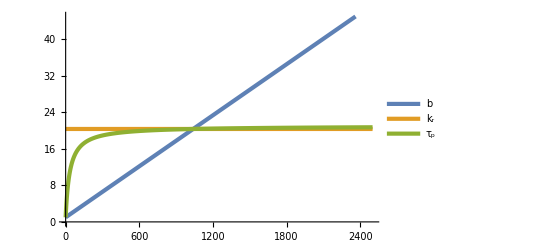

```mathematica
p2=Plot[{(gp/kr)*x/(1+gp/gr)+1,b/(1+gp/gr)+1,b/(1+kr*b/(gr*x))+1},{x,0,2500},PlotRange->{0,45},PlotStyle->AbsoluteThickness[3],PlotLegends->Placed[LineLegend[{"b","k_r","τ_p"},LegendMarkerSize->{30},LabelStyle->{FontFamily->"Palatino Linotype",40},LegendLayout->{"Row",3},Spacings->0.2],{0.88,0.2}]]
```

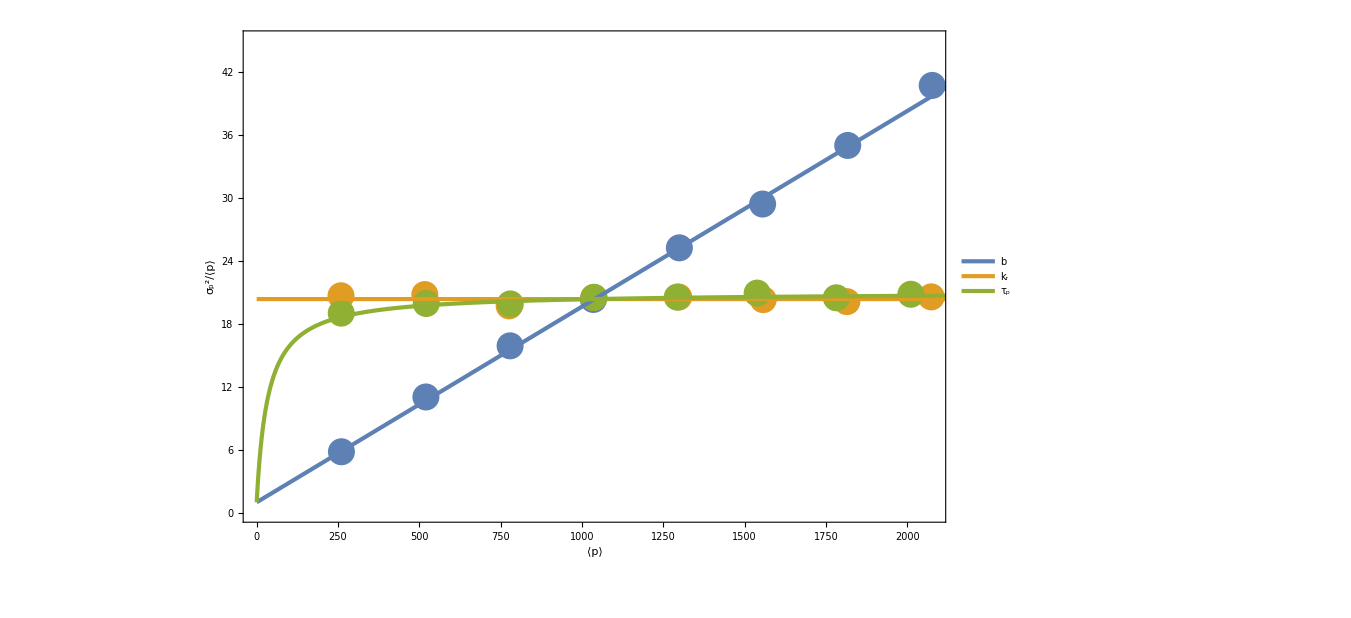

```mathematica
Show[p1,p2,ImageSize->1000,Frame->True,FrameStyle->Directive[Black,Thick],FrameLabel->{Text[Style[ToExpression["\\langle p\\rangle",TeXForm,HoldForm],40]],Text[Style[ToExpression["\\frac{\\sigma_p^2}{\\langle p\\rangle}",TeXForm,HoldForm],40]]},RotateLabel->False,LabelStyle->Directive[35,FontFamily->"Palatino Linotype",Black]]
```